# Elements of Mathematica’s Wolfram Language (version 23-09-2020)

### To run an input cell: shift + Enter

```mathematica
1+1
```

2

```mathematica
%
```

2

```mathematica
%+%%
```

4

```mathematica
N[Pi,5]
```

3.1416

```mathematica
%6
```

4

### Special characters by means of esc-esc

α
λ
δ
Δ
≠
 ≥
 ≤
 ⇒
 →
 ∧
 ¬
 ∨

```mathematica
a={11,22,33}
```

{11,22,33}

```mathematica
a⟦2⟧
```

22

```mathematica
2^4
```

16

## Writing functions: functionName[arguments]:= functionBody

### Definição de função (soma de dois números)

Underscore ( _ ) define um pattern.

```mathematica
Soma[a_Integer,b_Integer]:=a+b;
```

```mathematica
Soma[2,3]
```

5

```mathematica
Soma[2.0,3]
```

Soma[2.,3]

```mathematica
Soma[a_,b_]:=a+b;
```

```mathematica
Soma[2.0,3]
```

5.

```mathematica
Soma[{2,3,4,5},{5,6,7}]
```

{5,6,7}+{2,3,4,5}

```mathematica
?Soma
```

```mathematica
ClearAll@Soma
```

```mathematica
?Soma
```

### Função pura (soma 1 a um número)

```mathematica
SomaUm[a_]:=a+1;
```

```mathematica
SomaUm[2]
```

3

```mathematica
(#+1)&[2]
```

3

```mathematica
(#+1)&@2
```

3

### Fatorial (treinando recursão...)

```mathematica
Fat[0]:=1;
Fat[n_Integer/;n>0]:=n*Fat[n-1];
```

```mathematica
Fat[0]
```

1

```mathematica
Fat[-5]
```

Fat[-5]

```mathematica
Fat[8]
```

40320

## Some native functions

### Table

```mathematica
Table[a,5]
```

{a,a,a,a,a}

```mathematica
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[10i+j,{i,4},{j,3}]
```

{{11,12,13},{21,22,23},{31,32,33},{41,42,43}}

```mathematica
MatrixForm[%]
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33
41 | 42 | 43)

#### Números de 1 a 10

```mathematica
Table[x,{x,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

#### Quadrado dos números de 1 a 10

```mathematica
Table[x^2,{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

#### Fatorial dos números de 1 a 10

```mathematica
Table[Fat[x],{x,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

#### Pares ordenados com os números de 1 a 10 e seus quadrados

```mathematica
Table[{x,x^2},{x,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

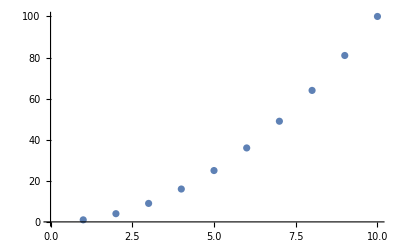

```mathematica
ListPlot[%]
```

#### Matriz 3 x 4 cujas células são a soma da linha com a coluna

```mathematica
Table[x+y,{x,1,3},{y,1,4}]
```

{{2,3,4,5},{3,4,5,6},{4,5,6,7}}

```mathematica
Table[x+y,{x,1,3},{y,1,4}]//MatrixForm
```

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

### Range, e RandomInteger

```mathematica
Range[0,9]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
RandomInteger[{0,1},10]
```

{1,0,1,1,1,0,0,1,1,1}

```mathematica
Table[RandomInteger[{0,1},10],5]  //MatrixForm
```

(0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

### Flatten

```mathematica
Flatten[{{{1,2,3}}}]
Flatten[{{{1,2,3}}},1]
```

{1,2,3}

{{1,2,3}}

```mathematica
Flatten[{{{1,2,3},{4,5}}}]
```

{1,2,3,4,5}

### Map (e sua notação infixada)

```mathematica
Sqrt@4
Sqrt[4]
```

2

2

```mathematica
Map[Sqrt,{1,4,9,16}]
Sqrt[#]&/@{1,4,9,16}
```

{1,2,3,4}

{1,2,3,4}

```mathematica
Map[SomaUm[#]&,Range[0,9]]
Map[SomaUm,Range[0,9]]
SomaUm[#]&/@Range[0,9]
SomaUm/@Range[0,9]
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

«1 more identical outputs»

```mathematica
Map[(#+1)&,Range[0,9]]
(#+1)&/@Range[0,9]
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[Length,{Range[0,9],Range[0,4]}]
Map[Length[#]&,{Range[0,9],Range[0,4]}]
Length/@{Range[0,9],Range[0,4]}
Length[#]&/@{Range[0,9],Range[0,4]}
```

{10,5}

{10,5}

{10,5}

«1 more identical outputs»

### MapThread

```mathematica
MapThread[Times,{{1,2,3,4,5},{5,6,7,8,9}}]
MapThread[Times[#1,#2]&,{{1,2,3,4,5},{5,6,7,8,9}}]
MapThread[Times[#2,#1]&,{{1,2,3,4,5},{5,6,7,8,9}}]
```

{5,12,21,32,45}

{5,12,21,32,45}

{5,12,21,32,45}

```mathematica
MapThread[List,{{1,2,3,4,5},{5,4,3,2,1},{a,b,c,d,f}}]
MapThread[List[#1,#2,#3]&,{{1,2,3,4,5},{5,4,3,2,1},{a,b,c,d,f}}]
```

{{1,5,a},{2,4,b},{3,3,c},{4,2,d},{5,1,f}}

{{1,5,a},{2,4,b},{3,3,c},{4,2,d},{5,1,f}}

### GatherBy, Select e Cases

```mathematica
EvenQ[5]
EvenQ[6]
```

False

True

```mathematica
GatherBy[Range[0,20],EvenQ]
GatherBy[Range[0,20],EvenQ[#]&]
```

{{0,2,4,6,8,10,12,14,16,18,20},{1,3,5,7,9,11,13,15,17,19}}

{{0,2,4,6,8,10,12,14,16,18,20},{1,3,5,7,9,11,13,15,17,19}}

```mathematica
Select[Range[0,20],EvenQ]
Select[Range[0,20],EvenQ[#]&]
```

{0,2,4,6,8,10,12,14,16,18,20}

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
Select[Range[0,20],If[OddQ[#],False,True]&]
```

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
MyEvenQ[x_Integer]:=If[OddQ[x],False,True];
```

```mathematica
Select[Range[0,20],MyEvenQ]
```

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
Cases[Range[0,20],x_/;EvenQ[x]]
```

{0,2,4,6,8,10,12,14,16,18,20}

### Position (dada uma lista de objetos quaisquer, encontrar as posições onde se encontram números inteiros maiores que 5)

```mathematica
listaobjetos={17,Graph[{1->2,2->3,3->1,3->4,4->1}],7,5.0,5,6,{6,7,9},"Olá!",1,-3,{1,2,3}};
```

```mathematica
Position[listaobjetos,x_Integer/;x>5]
```

{{1},{3},{6},{7,1},{7,2},{7,3}}

### Join, Union e Intersection

```mathematica
Join[{3,2},{2,1}]
```

{3,2,2,1}

```mathematica
Union[{3,2},{2,1}]
```

{1,2,3}

```mathematica
Intersection[{3,2},{2,1}]
```

{2}

### Associations

```mathematica
Association[{c->6,b->2,a->3}]
```

<|c→6,b→2,a→3|>

```mathematica
Normal[<|c->6,b->2,a->3|>]
```

{c→6,b→2,a→3}

```mathematica
Keys[<|c->6,b->2,a->3|>]
Values[<|c->6,b->2,a->3|>]
```

{c,b,a}

{6,2,3}

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

<|a→6,b→2,c→3|>

```mathematica
Tally[{a,a,b,c,a,a,b,c,c,a,a}]
```

{{a,6},{b,2},{c,3}}

```mathematica
<|a->6,b->2,c->3|>[c]
```

3

```mathematica
f/@<|a->6,b->2,c->3|>
```

<|a→f[6],b→f[2],c→f[3]|>

```mathematica
(f/@<|a->6,b->2,c->3|>)[a]
```

f[6]

```mathematica
(f/@<|a->6,b->2,c->3|>)[a]
```

### Regras de Substituição

#### Dada uma lista de números binários, trocar 0 por 1 e vice-versa

```mathematica
randomBitSequence=RandomInteger[1,20]
```

{1,1,0,0,1,0,0,0,1,0,1,0,1,1,1,1,1,0,1,1}

```mathematica
randomBitSequence/.{0->1,1->0}
1-randomBitSequence
```

{0,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,1,0,0}

{0,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,1,0,0}

#### Substituição com patterns

```mathematica
{{1,a},{1,b},{1,a,b,c},{2,b,c},{2,b}}/.{1,_}->Red
{{1,a},{1,b},{1,a,b,c},{2,b,c},{2,b}}/.{1,__}->Red
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],{1,a,b,c},{2,b,c},{2,b}}

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],{2,b,c},{2,b}}

#### Dada uma lista de números binários, trocar 0 por um grafo, e 1 por 0)

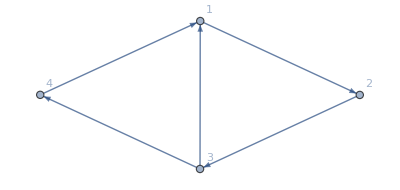
{0,-Graphics-,0,-Graphics-,-Graphics-,-Graphics-,0,-Graphics-,-Graphics-,0,0,-Graphics-,-Graphics-,-Graphics-,0,0,0,-Graphics-,-Graphics-,-Graphics-}

```mathematica
randomBitSequence/.{0->Graph[{1->2,2->3,3->1,3->4,4->1},VertexLabels->"Name"],1->0}
```

#### Dada uma lista de números inteiros, trocar todos os pares por 0 e todos os ímpares por 1

```mathematica
listaInt=RandomInteger[10,20]
```

{7,2,6,5,10,3,2,2,6,8,0,8,0,7,1,7,0,2,9,4}

```mathematica
listaInt/.{x_/;EvenQ[x]->0,x_/;OddQ[x]->1}
```

{1,0,0,1,0,1,0,0,0,0,0,0,0,1,1,1,0,0,1,0}

### Head

```mathematica
Head[5]
```

Integer

```mathematica
Head[5.0]
```

Real

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[2+3+4]
```

Integer

```mathematica
Head[True]
```

Symbol

```mathematica
Head["Boa noite!"]
```

String

```mathematica
Head[x]
```

Symbol

```mathematica
x=5;
Head[x]
```

Integer

```mathematica
ClearAll[x]
```

```mathematica
Module[{x},
x=5;
x=4;
x=3]
```

3

```mathematica
x
```

x

```mathematica
FullForm[{1,2,3}]
FullForm[List[1,2,3]]
```

List[1,2,3]

List[1,2,3]

### Apply[f, expression] (troca a Head de expression por f]

```mathematica
Apply[f,{1,2,3}]
f@@{1,2,3}
```

f[1,2,3]

f[1,2,3]

```mathematica
Apply[Sqrt,{1,4,9,16}]
Sqrt@@{1,4,9,16}
```

Sqrt[1,4,9,16]

Sqrt[1,4,9,16]

```mathematica
Apply[OddQ,{5}]
OddQ@@{5}
```

True

True

```mathematica
Times[1,2,3,4]
Apply[Times,{1,2,3,4}]
Times@@{1,2,3,4}
```

24

24

24

### CellularAutomaton

```mathematica
CellularAutomaton[{110,2,1},{0,1,0,0,0,0,0,0,0},10]
```

{{0,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,1},{0,1,0,0,0,1,1,0,0},{1,1,0,0,1,1,1,0,0},{1,1,0,1,1,0,1,0,1},{0,1,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1}}

```mathematica
CellularAutomaton[{110,2,1},{0,1,0,0,0,0,0,0,0},10]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

```mathematica
CellularAutomaton[{110,2,1},{{1},0},3]
```

{{0,0,0,1},{0,0,1,1},{0,1,1,1},{1,1,0,1}}

```mathematica
CellularAutomaton[{110,2,1},{{1},0},10]
```

{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,1,1,0,0,0,1},{0,0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,0,1,0,1,1,1},{0,0,1,1,1,1,1,1,1,0,1},{0,1,1,0,0,0,0,0,1,1,1},{1,1,1,0,0,0,0,1,1,0,1}}

```mathematica
CellularAutomaton[{110,2,1},{{1},0},10]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1)

```mathematica
ArrayPlot[CellularAutomaton[{110,2,1},RandomInteger[{0,1},100],100]]
```

-Graphics-

### RulePlot

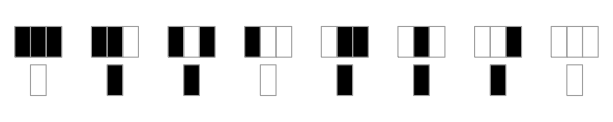

```mathematica
RulePlot[CellularAutomaton[{110,2,1}]]
```

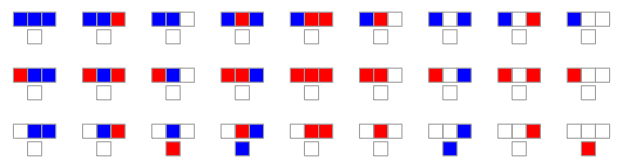

```mathematica
RulePlot[CellularAutomaton[{1234,3}],ColorRules->{0->White,1->Red,_->Blue}]
```

### Visualização de conjunto de evoluções temporais

```mathematica
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},50],100],PlotLabel->#]&/@Range[0,255],16]]
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},50],100]]&/@Range[0,16]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Execução do AC da FCI (binário, bidimensional)

```mathematica
{{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}//MatrixForm
```

(a_ | b_ | c_
d_ | e_ | f_
g_ | h_ | i_)

```mathematica
testRule={{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}->Mod[b+d+e+f+h,2];
```

```mathematica
testRule={{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}->Mod[a+b+c+d+e+f+g+h+i,2]
```

```mathematica
ArrayPlot[#]&/@CellularAutomaton[
      { (#/.testRule)&,
        {},
        {1,1}
        },fciIC,32]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[ArrayPlot[#]&/@CellularAutomaton[
      { (#/.testRule)&,
        {},
        {1,1}
        },fciIC,32],AnimationRate->1]
```

```mathematica
ListAnimate[ArrayPlot[{#}]&/@CellularAutomaton[{110,2,1},RandomInteger[{0,1},100],100],AnimationRate->1]
```

## Some functions from CAMaT.nb

### RuleTable

#### Symmetrical neighbourhoods

```mathematica
RuleTable[110]
%//MatrixForm
```

{{{1,1,1},0},{{1,1,0},1},{{1,0,1},1},{{1,0,0},0},{{0,1,1},1},{{0,1,0},1},{{0,0,1},1},{{0,0,0},0}}

({1,1,1} | 0
{1,1,0} | 1
{1,0,1} | 1
{1,0,0} | 0
{0,1,1} | 1
{0,1,0} | 1
{0,0,1} | 1
{0,0,0} | 0)

```mathematica
RuleTable[4412,3,1]//MatrixForm
```

({2,2,2} | 0
{2,2,1} | 0
{2,2,0} | 0
{2,1,2} | 0
{2,1,1} | 0
{2,1,0} | 0
{2,0,2} | 0
{2,0,1} | 0
{2,0,0} | 0
{1,2,2} | 0
{1,2,1} | 0
{1,2,0} | 0
{1,1,2} | 0
{1,1,1} | 0
{1,1,0} | 0
{1,0,2} | 0
{1,0,1} | 0
{1,0,0} | 0
{0,2,2} | 0
{0,2,1} | 2
{0,2,0} | 0
{0,1,2} | 0
{0,1,1} | 0
{0,1,0} | 1
{0,0,2} | 1
{0,0,1} | 0
{0,0,0} | 2)

#### Asymmetrical neighbourhoods: no central cell; reference cell displaced to the right

```mathematica
RuleTable[2410,2,1.5]//MatrixForm
```

({1,1,1,1} | 0
{1,1,1,0} | 0
{1,1,0,1} | 0
{1,1,0,0} | 0
{1,0,1,1} | 1
{1,0,1,0} | 0
{1,0,0,1} | 0
{1,0,0,0} | 1
{0,1,1,1} | 0
{0,1,1,0} | 1
{0,1,0,1} | 1
{0,1,0,0} | 0
{0,0,1,1} | 1
{0,0,1,0} | 0
{0,0,0,1} | 1
{0,0,0,0} | 0)

```mathematica
RuleTable[10,2,0.5]//MatrixForm
```

({1,1} | 1
{1,0} | 0
{0,1} | 1
{0,0} | 0)

### RnumFromRuleTable

```mathematica
RnumFromRuleTable[RuleTable[110]]
```

110

```mathematica
RnumFromRuleTable[RuleTable[4412,3,1],3]
```

4412

```mathematica
RnumFromRuleTable[RuleTable[2410,2,1.5],2]
```

2410

### FlexRadius

```mathematica
FlexRadius[1]
FlexRadius[1.]
FlexRadius[1.5]
```

1

1

{{-2},{-1},{0},{1}}

```mathematica
ArrayPlot@CellularAutomaton[{3450,2,FlexRadius[1.5]},{{1},0},100]
ArrayPlot@CellularAutomaton[{3450,2,{{-2},{-1},{0},{1}}},{{1},0},100]
```

-Graphics-

-Graphics-